# DATI DEL SISTEMA PROPRIO LTI-TC

```mathematica
ClearAll["Global`*"]
```

```mathematica
A = {{0, -2, 2, -1}, {-271/4, -623, 1063/4, -1349/4}, {-271/4, -626, 1071/4, -1357/4}, {275/4, 622, -1059/4, 1345/4}}; A//MatrixForm
```

(0 | -2 | 2 | -1
-271/4 | -623 | 1063/4 | -1349/4
-271/4 | -626 | 1071/4 | -1357/4
275/4 | 622 | -1059/4 | 1345/4)

```mathematica
B = {{0}, {-1}, {-1}, {1}}; B//MatrixForm
```

(0
-1
-1
1)

```mathematica
Subscript[C, 1] = {{-8, 4, 2, 6}}; Subscript[C, 1]//MatrixForm
```

(-8 | 4 | 2 | 6)

## 1. Ricerca dei modi naturali del sistema

```mathematica
λ = Eigenvalues[A]
```

{-8,-7,-2+ⅈ/2,-2-ⅈ/2}

```mathematica
σ=Re[λ[[3]]]
```

-2

```mathematica
ω=Im[λ[[3]]]
```

1/2

```mathematica
CharacteristicPolynomial[A, x]
```

238+(1151 x)/4+(481 x^2)/4+19 x^3+x^4

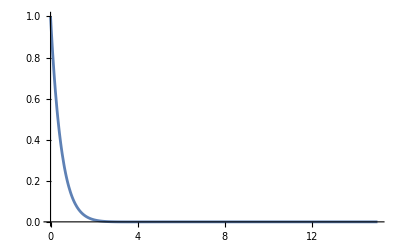

```mathematica
Plot[Exp[σ t]Cos[ω t],{t,0,15},PlotRange->All]
```

Abbiamo trovato autovalori  reali i cui modi sono e^(-8t) e e^(-7t) dobbiamo trovare ora i modi dei nostri autovalori  immaginari pari a -2 +- j 
Scriviamo la matrice di cambiamento di Base

```mathematica
Subscript[T, 0]=Transpose[Eigenvectors[A]]
```

{{63/646,24/223,3792/19433+(34 ⅈ)/19433,3792/19433-(34 ⅈ)/19433},{-291/323,-397/446,-14745/19433+(698 ⅈ)/19433,-14745/19433-(698 ⅈ)/19433},{-511/646,-171/223,-8829/19433+(1612 ⅈ)/19433,-8829/19433-(1612 ⅈ)/19433},{1,1,1,1}}

```mathematica
Subscript[T, 0]//MatrixForm
```

(63/646 | 24/223 | 3792/19433+(34 ⅈ)/19433 | 3792/19433-(34 ⅈ)/19433
-291/323 | -397/446 | -14745/19433+(698 ⅈ)/19433 | -14745/19433-(698 ⅈ)/19433
-511/646 | -171/223 | -8829/19433+(1612 ⅈ)/19433 | -8829/19433-(1612 ⅈ)/19433
1 | 1 | 1 | 1)

```mathematica
T =Transpose[{Subscript[T, 0][[All,1]], Subscript[T, 0][[All,2]],Re[Subscript[T, 0][[All,3]]], Im[Subscript[T, 0][[All,3]]]}]
```

{{63/646,24/223,3792/19433,34/19433},{-291/323,-397/446,-14745/19433,698/19433},{-511/646,-171/223,-8829/19433,1612/19433},{1,1,1,0}}

```mathematica
T//MatrixForm
```

(63/646 | 24/223 | 3792/19433 | 34/19433
-291/323 | -397/446 | -14745/19433 | 698/19433
-511/646 | -171/223 | -8829/19433 | 1612/19433
1 | 1 | 1 | 0)

```mathematica
Λ = Simplify[Inverse[T].A.T]
```

{{-8,0,0,0},{0,-7,0,0},{0,0,-2,1/2},{0,0,-1/2,-2}}

```mathematica
Λ//MatrixForm
```

(-8 | 0 | 0 | 0
0 | -7 | 0 | 0
0 | 0 | -2 | 1/2
0 | 0 | -1/2 | -2)

```mathematica
MatrixExp[Λ t]//MatrixForm
```

(ⅇ^(-8 t) | 0 | 0 | 0
0 | ⅇ^(-7 t) | 0 | 0
0 | 0 | ⅇ^(-2 t) Cos[t/2] | ⅇ^(-2 t) Sin[t/2]
0 | 0 | -ⅇ^(-2 t) Sin[t/2] | ⅇ^(-2 t) Cos[t/2])

## 2. Calcolo della risposta libera

```mathematica
Subscript[x, 0]={{2}, {0}, {3}, {-2}}
```

{{2},{0},{3},{-2}}

```mathematica
Subscript[x, 0]//MatrixForm
```

(2
0
3
-2)

Proietto lo stato iniziale lungo le colonne della matrice “ibrida” T

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{85918/29},{-337622/101},{1107462/2929},{-3175885/5858}}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

((ⅇ^(-8 t) (846279-1053744 ⅇ^t+213323 ⅇ^(6 t) Cos[t/2]-311796 ⅇ^(6 t) Sin[t/2]))/2929
(ⅇ^(-8 t) (-15636012+17430682 ⅇ^t-1794670 ⅇ^(6 t) Cos[t/2]+2330181 ⅇ^(6 t) Sin[t/2]))/5858
(ⅇ^(-8 t) (38 (-361277+395154 ⅇ^t)-1269752 ⅇ^(6 t) Cos[t/2]+1259169 ⅇ^(6 t) Sin[t/2]))/5858
(ⅇ^(-8 t) (17355436-19582076 ⅇ^t+2214924 ⅇ^(6 t) Cos[t/2]-3175885 ⅇ^(6 t) Sin[t/2]))/5858)

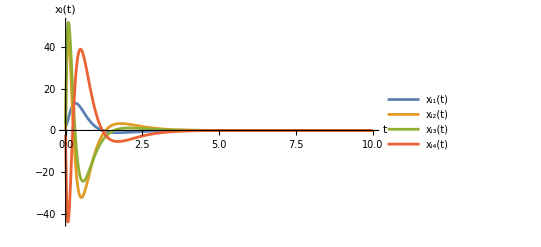

```mathematica
Plot[{Subscript[x, l][t][[1]],Subscript[x, l][t][[2]],Subscript[x, l][t][[3]],Subscript[x, l][t][[4]]}, {t, 0,10}, PlotRange->All, AxesLabel->{t,"x_l(t)"}, PlotLegends->{"x_l1(t)","x_l2(t)","x_l3(t)","x_l4(t)"}]
```

## 3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

```mathematica
Subscript[x, 01]=Transpose[T][[1]]
```

{63/646,-291/323,-511/646,1}

```mathematica
Subscript[z, 01]=Inverse[T].Subscript[x, 01]
```

{1,0,0,0}

```mathematica
Subscript[x, 02]=Transpose[T][[2]]
```

{24/223,-397/446,-171/223,1}

```mathematica
Subscript[z, 02]=Inverse[T].Subscript[x, 02]
```

{0,1,0,0}

```mathematica
Subscript[x, 03]=Transpose[T][[3]]
```

{3792/19433,-14745/19433,-8829/19433,1}

```mathematica
Subscript[z, 03]=Inverse[T].Subscript[x, 03]
```

{0,0,1,0}

```mathematica
Subscript[x, 04]=Transpose[T][[4]]
```

{34/19433,698/19433,1612/19433,0}

```mathematica
Subscript[z, 04]=Inverse[T].Subscript[x, 04]
```

{0,0,0,1}

## 4. Ricerca della Fdt, poli e zeri

```mathematica
G[s_] := Simplify[Subscript[C, 1].Inverse[s IdentityMatrix[4]-A].B]
```

```mathematica
G[s][[1,1]]
```

(8 (-3+s))/(952+1151 s+481 s^2+76 s^3+4 s^4)

Verifichiamo che il calcolo della funzione di trasferimento è corretto facendo uso del modello della funzione di traferimento:

```mathematica
Σ = StateSpaceModel[{A,B, Subscript[C, 1]}]
```

0-22-10-271/4-6231063/4-1349/4-1-271/4-6261071/4-1357/4-1275/4622-1059/41345/41-84260StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

(-6+2 s)/(238+(1151 s)/4+(481 s^2)/4+19 s^3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-62381FalseFalseFalseAutomaticNoneAutomatic

Calcolo dei poli

```mathematica
Solve[Denominator[G[s][[1]]]==0, s]
```

{{s→-8},{s→-7},{s→-2-ⅈ/2},{s→-2+ⅈ/2}}

```mathematica
λ
```

{-8,-7,-2+ⅈ/2,-2-ⅈ/2}

possiamo notare che gli autovalori della Matrice A  sono uguali agli zeri del denominatore

Verifichiamo facendo sempre uso della funzione del modello della funzione di trasferimento che i nostri risultati risultano corretti:

```mathematica
TransferFunctionPoles[Σ]
```

{{{-8,-7,-2-ⅈ/2,-2+ⅈ/2}}}

Calcolo degli zeri

```mathematica
Solve[Numerator[G[s][[1]]]==0, s]
```

{{s→3}}

Verifichiamo facendo sempre uso della funzione del modello della funzione di trasferimento che i nostri risultati risultano corretti:

```mathematica
TransferFunctionZeros[Σ]
```

{{{3}}}

## 5. Calcolo della risposta al gradino

Riprendiamo in considerazione la nostra funzione di trasferiemento

```mathematica
G[s][[1,1]]
```

(8 (-3+s))/(952+1151 s+481 s^2+76 s^3+4 s^4)

```mathematica
Subscript[Y, f][s_] := Factor[G[s][[1,1]]LaplaceTransform[UnitStep[t], t, s]]
```

```mathematica
Subscript[Y, f][s]
```

(8 (-3+s))/(s (7+s) (8+s) (17+16 s+4 s^2))

```mathematica
Apart[Subscript[Y, f][s]]
```

-3/(119 s)+80/(707 (7+s))-11/(145 (8+s))-(32 (-4259+376 s))/(248965 (17+16 s+4 s^2))

Scrivo in maniera verbosa i frassi semplici

```mathematica
C1/s+Subscript[C, 2]/(7+s)+Subscript[C, 3]/(8+s)+Subscript[C, 4]/(s+2+ⅈ/2)+Subscript[C, 5]/(s+2-ⅈ/2)
```

C1/s-(1504/248965+(40088 ⅈ)/248965)/((2-ⅈ/2)+s)-(1504/248965-(40088 ⅈ)/248965)/((2+ⅈ/2)+s)+80/(707 (7+s))-11/(145 (8+s))

```mathematica
C1=G[0][[1,1]]
```

-3/119

```mathematica
Subscript[C, 2]=lim_(s->-7) (7+s)Subscript[Y, f][s]
```

80/707

```mathematica
Subscript[C, 3]=lim_(s->-8) (8+s)Subscript[Y, f][s]
```

-11/145

```mathematica
Subscript[C, 4]=lim_(s->-2-ⅈ/2) (s+2+ⅈ/2)Subscript[Y, f][s]
```

-1504/248965+(40088 ⅈ)/248965

```mathematica
Subscript[C, 5]=Conjugate[Subscript[C, 4]]
```

-1504/248965-(40088 ⅈ)/248965

```mathematica
F[Z_,γ_,t_]:= ComplexExpand[Re[Z Exp[I γ t]]]
```

```mathematica
Subscript[Y, f][t_]:=C1 UnitStep[t]+Subscript[C, 2] Exp[-7t]UnitStep[t]+Subscript[C, 3] Exp[-8t]UnitStep[t]+2Exp[-2t]F[Subscript[C, 4],-1/2,t]UnitStep[t];Subscript[Y, f][t]
```

-(3 UnitStep[t])/119-11/145 ⅇ^(-8 t) UnitStep[t]+80/707 ⅇ^(-7 t) UnitStep[t]+2 ⅇ^(-2 t) (-(1504 Cos[t/2])/248965+(40088 Sin[t/2])/248965) UnitStep[t]

```mathematica
FullSimplify[Subscript[Y, f][t]-(-3/119-(11 ⅇ^(-8 t))/145+(80 ⅇ^(-7 t))/707-(1504/248965-(40088 ⅈ)/248965) ⅇ^((-2-ⅈ/2) t)-(1504/248965+(40088 ⅈ)/248965) ⅇ^((-2+ⅈ/2) t))UnitStep[t]]
```

0

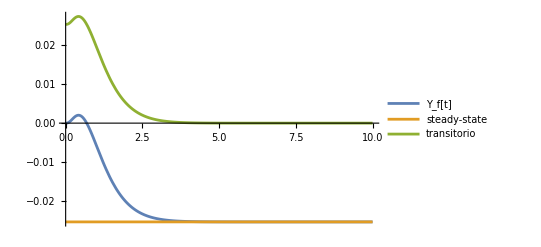

```mathematica
Plot[{Subscript[Y, f][t],-3/119 UnitStep[t],-11/145 ⅇ^(-8 t) UnitStep[t]+80/707 ⅇ^(-7 t) UnitStep[t]+2 ⅇ^(-2 t) (-(1504 Cos[t/2])/248965+(40088 Sin[t/2])/248965) UnitStep[t]}, {t, 0,10}, PlotRange->All,PlotLegends->{"Y_f[t]","steady-state","transitorio"}]
```

```mathematica
Subscript[Y, f][t]/.{t->0}
```

0

## 6. Risposta al segnale periodico elementare u(t)=Asin(ωt+ψ)1(t)

Prendo come valori Α = 1, ω = 1 e ψ = 0

```mathematica
Α = 1
```

1

```mathematica
ω = 1
```

1

```mathematica
ψ = 0
```

0

```mathematica
Subscript[u, segnale][t_] := Α  Sin[ω t + ψ]
```

```mathematica
U[s_] = LaplaceTransform[Subscript[u, segnale][t] * UnitStep[t], t, s]
```

1/(1+s^2)

```mathematica
G[s][[1,1]]
```

(8 (-3+s))/(952+1151 s+481 s^2+76 s^3+4 s^4)

```mathematica
U[s]
```

1/(1+s^2)

```mathematica
Subscript[y, segnalef][s_]:=Factor[G[s] * U[s]][[1,1]]
```

```mathematica
Subscript[y, segnalef][s]
```

(8 (-3+s))/((7+s) (8+s) (1+s^2) (17+16 s+4 s^2))

```mathematica
Apart[Subscript[y, segnalef][s]]
```

-8/(505 (7+s))+88/(9425 (8+s))+(8 (-7+74 s))/(27625 (1+s^2))-(128 (18258+2903 s))/(6224125 (17+16 s+4 s^2))

```mathematica
Solve[1+s^2 == 0, s]
```

{{s→-ⅈ},{s→ⅈ}}

```mathematica
Subscript[D, 1]/(s+ⅈ)+Subscript[D, 2]/(s-ⅈ)+Subscript[D, 3]/(s+7)+Subscript[D, 4]/(8+s)+Subscript[D, 5]/(s+2+ⅈ/2)+Subscript[D, 6]/(s+2-ⅈ/2)
```

(296/27625-(28 ⅈ)/27625)/(-ⅈ+s)+(296/27625+(28 ⅈ)/27625)/(ⅈ+s)-(46448/6224125-(398464 ⅈ)/6224125)/((2-ⅈ/2)+s)-(46448/6224125+(398464 ⅈ)/6224125)/((2+ⅈ/2)+s)-8/(505 (7+s))+88/(9425 (8+s))

```mathematica
Subscript[D, 1]=lim_(s->ⅈ) (s-ⅈ) Subscript[y, segnalef][s]
```

296/27625+(28 ⅈ)/27625

```mathematica
Subscript[D, 2]=Conjugate[Subscript[D, 1]]
```

296/27625-(28 ⅈ)/27625

```mathematica
Subscript[D, 3]=lim_(s->-7) (7+s) Subscript[y, segnalef][s]
```

-8/505

```mathematica
Subscript[D, 4]=lim_(s->-8) (8+s) Subscript[y, segnalef][s]
```

88/9425

```mathematica
Subscript[D, 5]=lim_(s->-2-ⅈ/2) (s+2+ⅈ/2) Subscript[y, segnalef][s]
```

-46448/6224125-(398464 ⅈ)/6224125

```mathematica
Subscript[D, 6]=Conjugate[Subscript[D, 5]]
```

-46448/6224125+(398464 ⅈ)/6224125

```mathematica
Subscript[D, 1]/(s+3ⅈ)+Subscript[D, 2]/(s-3ⅈ)+Subscript[D, 3]/(s+7)+Subscript[D, 4]/(8+s)+Subscript[D, 5]/(s+2+ⅈ/2)+Subscript[D, 6]/(s+2-ⅈ/2)
```

(296/27625-(28 ⅈ)/27625)/(-3 ⅈ+s)+(296/27625+(28 ⅈ)/27625)/(3 ⅈ+s)-(46448/6224125-(398464 ⅈ)/6224125)/((2-ⅈ/2)+s)-(46448/6224125+(398464 ⅈ)/6224125)/((2+ⅈ/2)+s)-8/(505 (7+s))+88/(9425 (8+s))

```mathematica
F[Z_,γ_,t_]:= ComplexExpand[Re[Z Exp[I γ t]]]
```

```mathematica
Subscript[Y, ss][t_] := 2 ComplexExpand[F[Subscript[D, 1],2,t]]
Subscript[Y, ss][t]
```

2 ((296 Cos[2 t])/27625-(28 Sin[2 t])/27625)

```mathematica
InverseLaplaceTransform[Subscript[y, segnalef][s],s,t]
```

8 ((11 ⅇ^(-8 t))/9425-ⅇ^(-7 t)/505-(2 ⅇ^((-2-ⅈ/2) t) ((2903+24904 ⅈ)+(2903-24904 ⅈ) ⅇ^(ⅈ t)))/6224125+(74 Cos[t]-7 Sin[t])/27625)

```mathematica
Solve[{(2 ((296 Cos[2 t])/27625+(28 Sin[2 t])/27625) == Ampiezza Sin[ω*t+angolo]) /. {t->0}, (D[2 ((296 Cos[2 t])/27625+(28 Sin[2 t])/27625) ,t] == D [Ampiezza Sin[ω*t+angolo], t]) /. {t->0}, Ampiezza > 0}, {Ampiezza, angolo}]
```

{{Ampiezza→ConditionalExpression[(16 √1418)/27625, C[1]∈ℤ],angolo→ConditionalExpression[-2 ArcTan[(-1418+7 √1418)/(37 √1418)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
N[(16 √1418)/27625]
```

0.02181

```mathematica
N[-2 ArcTan[(-1418+7 √1418)/(37 √1418)]](180/π)
```

79.2869

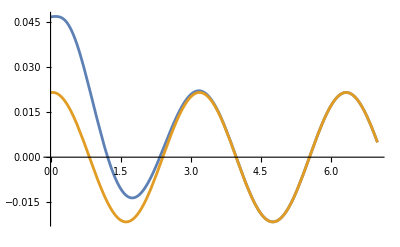

```mathematica
Plot[{-11/145 ⅇ^(-8 t) UnitStep[t]+80/707 ⅇ^(-7 t) UnitStep[t]+2 ⅇ^(-2 t) (-(1504 Cos[t/2])/248965+(40088 Sin[t/2])/248965) UnitStep[t]+2 ((296 Cos[2 t])/27625+(28 Sin[2 t])/27625),2 ((296 Cos[2 t])/27625+(28 Sin[2 t])/27625)},{t,0,7},PlotRange->All]
```

## 7. Modello ARMA equivalente

Prendiamo in considerazione le seguenti condizioni iniziali sull’uscita compatibili con lo stato iniziale.

```mathematica
Subscript[x, condARMA] = {{0}, {-2}, {-2}, {-1}}
```

{{0},{-2},{-2},{-1}}

```mathematica
Subscript[y, condArmaIU]=(Subscript[C, 1][[1]] Subscript[x, condARMA])[[1]]
```

{0}

```mathematica
Subscript[y', condArmaIU]=(Subscript[C, 1][[1]].A.Subscript[x, condARMA])[[1]]
```

6

```mathematica
Subscript[y'', condArmaIU]=(Subscript[C, 1][[1]].A.A.Subscript[x, condARMA])[[1]]
```

-20

```mathematica
Subscript[y''', condArmaIU]=(Subscript[C, 1][[1]].A.A.A.Subscript[x, condARMA])[[1]]
```

-4211/2

```mathematica
identità = Expand[Denominator[G[s][[1,1]]]Subscript[Y, arma][s]] == Expand[Numerator[G[s][[1,1]]]Subscript[U, arma][s]]
```

952 Y_arma[s]+1151 s Y_arma[s]+481 s^2 Y_arma[s]+76 s^3 Y_arma[s]+4 s^4 Y_arma[s]==-24 U_arma[s]+8 s U_arma[s]

```mathematica
InverseLaplaceTransform[identità, s, t] /. {Subscript[Y, arma][s] -> LaplaceTransform[ yarma[t], t, s],Subscript[U, arma][s]-> LaplaceTransform[uarma[t], t, s]} /. {yarma[0]-> 0, yarma'[0] -> 0, yarma''[0]-> 0, yarma'''[0]-> 0, uarma[0]->0}
```

952 yarma[t]+1151 yarma'[t]+481 yarma''[t]+76 yarma^(3)[t]+4 yarma^(4)[t]==-24 uarma[t]+8 uarma'[t]

```mathematica
eqdiff=952 yarma[t]+1151 yarma'[t]+481 yarma''[t]+76 Derivative[3][yarma][t]+4 Derivative[4][yarma][t]==-24 uarma[t]+8 uarma'[t]
```

952 yarma[t]+1151 yarma'[t]+481 yarma''[t]+76 yarma^(3)[t]+4 yarma^(4)[t]==-24 uarma[t]+8 uarma'[t]

```mathematica
eqdiffs = Simplify[LaplaceTransform[eqdiff, t, s] /. {yarma[t] -> InverseLaplaceTransform[Subscript[Y, arma][s],s,t], uarma[t] -> InverseLaplaceTransform[Subscript[U, arma][s],s,t],uarma[0]->0}]
```

(952+1151 s+481 s^2+76 s^3+4 s^4) Y_arma[s]==(1151+481 s+76 s^2+4 s^3) yarma[0]+8 (-3+s) U_arma[s]+481 yarma'[0]+76 s yarma'[0]+4 s^2 yarma'[0]+76 yarma''[0]+4 s yarma''[0]+4 yarma^(3)[0]

```mathematica
Subscript[Y, dif][s_] := Collect[Solve[eqdiffs, Subscript[Y, arma][s]][[1,1]][[2]], Subscript[U, arma][s]]
```

```mathematica
Subscript[Y, dif][s]
```

((-24+8 s) U_arma[s])/(952+1151 s+481 s^2+76 s^3+4 s^4)+(1151 yarma[0]+481 s yarma[0]+76 s^2 yarma[0]+4 s^3 yarma[0]+481 yarma'[0]+76 s yarma'[0]+4 s^2 yarma'[0]+76 yarma''[0]+4 s yarma''[0]+4 yarma^(3)[0])/(952+1151 s+481 s^2+76 s^3+4 s^4)

```mathematica
RispostaLiberaArma = ((1151 yarma[0]+481 s yarma[0]+76 s^2 yarma[0]+4 s^3 yarma[0]+481 yarma'[0]+76 s yarma'[0]+4 s^2 yarma'[0]+76 yarma''[0]+4 s yarma''[0]+4 Derivative[3][yarma][0])/(952+1151 s+481 s^2+76 s^3+4 s^4))/.{yarma[0] ->Subscript[y, condArmaIU],yarma'[0]->Subscript[y', condArmaIU], yarma''[0]->Subscript[y'', condArmaIU],yarma'''[0]-> Subscript[y''', condArmaIU]}
```

{(-7056+376 s+24 s^2)/(952+1151 s+481 s^2+76 s^3+4 s^4)}

```mathematica
Subscript[U, ru][s_]=LaplaceTransform[t UnitStep[t],t,s]
```

1/s^2

```mathematica
((-24+8 s) (1/s^2))/(952+1151 s+481 s^2+76 s^3+4 s^4)+(1151 *0+481 s *0+76 s^2 *0+4 s^3 *0+481 *6+76 s *6+4 s^2 *6+76 *(-20)+4 s *(-20)+4 (-4211/2))/(952+1151 s+481 s^2+76 s^3+4 s^4)
```

(-24+8 s)/(s^2 (952+1151 s+481 s^2+76 s^3+4 s^4))+(-7056+376 s+24 s^2)/(952+1151 s+481 s^2+76 s^3+4 s^4)

```mathematica
Subscript[Y, rampaUnitariaArma][t_]:=InverseLaplaceTransform[(-24+8 s)/(s^2 (952+1151 s+481 s^2+76 s^3+4 s^4))+(-7056+376 s+24 s^2)/(952+1151 s+481 s^2+76 s^3+4 s^4),s,t]
```

```mathematica
Subscript[Y, rampaUnitariaArma][t]
```

4405/113288+(13647 ⅇ^(-8 t))/232-(417168 ⅇ^(-7 t))/4949+(2 ⅇ^((-2-ⅈ/2) t) ((5381764-26486333 ⅈ)+(5381764+26486333 ⅈ) ⅇ^(ⅈ t)))/846481-(3 t)/119

```mathematica
Subscript[Y, componenteRegime]=-(3 t)/119+4405/113288
```

4405/113288-(3 t)/119

```mathematica
Subscript[Y, componenteTransitoria]=+(13647 ⅇ^(-8 t))/232-(417168 ⅇ^(-7 t))/4949+(2 ⅇ^((-2-ⅈ/2) t) ((5381764-26486333 ⅈ)+(5381764+26486333 ⅈ) ⅇ^(ⅈ t)))/846481
```

(13647 ⅇ^(-8 t))/232-(417168 ⅇ^(-7 t))/4949+(2 ⅇ^((-2-ⅈ/2) t) ((5381764-26486333 ⅈ)+(5381764+26486333 ⅈ) ⅇ^(ⅈ t)))/846481

## 8. Determinare lo stato inziale x_0 tale che la risposta al gradino concida con il suo valore di regime (assenza di componente transitoria)

Consideriamo la risposta forzata al gradino unitario pari a:

```mathematica
rispostaForzata :=G[s][[1,1]]/s
```

```mathematica
rispostaForzata
```

(8 (-3+s))/(s (952+1151 s+481 s^2+76 s^3+4 s^4))

La componente transitoria della risposta forzata sarà pari a:

```mathematica
Subscript[Y, componenteTransitoriaRisF][s_]:=FullSimplify[rispostaForzata-G[0][[1,1]]/s]
```

```mathematica
Subscript[Y, componenteTransitoriaRisF][s]
```

(4405+3 s (481+4 s (19+s)))/(119 (7+s) (8+s) (17+4 s (4+s)))

```mathematica
Subscript[x, statoIniziale7]={{x1},{x2},{x3},{x4}}
```

{{x1},{x2},{x3},{x4}}

```mathematica
rispostaLiberaGradino[s_]:=Simplify[Subscript[C, 1].Inverse[s IdentityMatrix[4]-A].Subscript[x, statoIniziale7]][[1,1]]
```

```mathematica
rispostaLiberaGradino[s]
```

(-4 (1475+850 s+146 s^2+8 s^3) x1+4 (3032+565 s+80 s^2+4 s^3) x2-2862 x3+498 s x3+128 s^2 x3+8 s^3 x3+9242 x4+2766 s x4+448 s^2 x4+24 s^3 x4)/(952+1151 s+481 s^2+76 s^3+4 s^4)

```mathematica
Numerator[Simplify[Expand[rispostaLiberaGradino[s]+Subscript[Y, componenteTransitoriaRisF][s]]]]
```

4405-702100 x1+1443232 x2-340578 x3+1099798 x4+4 s^3 (3-952 x1+476 x2+238 x3+714 x4)+4 s^2 (57-17374 x1+9520 x2+3808 x3+13328 x4)+s (1443-404600 x1+268940 x2+59262 x3+329154 x4)

```mathematica
CoefficientList[Numerator[Simplify[Expand[rispostaLiberaGradino[s]+Subscript[Y, componenteTransitoriaRisF][s]]]],s]
```

{4405-702100 x1+1443232 x2-340578 x3+1099798 x4,1443-404600 x1+268940 x2+59262 x3+329154 x4,4 (57-17374 x1+9520 x2+3808 x3+13328 x4),4 (3-952 x1+476 x2+238 x3+714 x4)}

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[rispostaLiberaGradino[s]+Subscript[Y, componenteTransitoriaRisF][s]]]],s]=={0,0,0,0},{x1,x2,x3,x4}]
```

{{x1→1/238,x2→-1/119,x3→-1/238,x4→1/119}}

## 9. Valutare la risposta al segnale u(t)=1(-t)

```mathematica
Subscript[M, O]={Subscript[C, 1][[1]],(Subscript[C, 1].A)[[1]],(Subscript[C, 1].A.A)[[1]],(Subscript[C, 1].A.A.A)[[1]]}
```

{{-8,4,2,6},{6,4,-6,-2},{-2,8,-2,8},{287/2,1248,-1063/2,1345/2}}

Verifico se la matrice è invertibile

```mathematica
Det[Subscript[M, O]]
```

44440

```mathematica
Subscript[Y, liberas]=FullSimplify[(Subscript[C, 1].Inverse[s IdentityMatrix[4]-A].Subscript[x, condARMA])[[1,1]]]
```

-(2 (13887+s (4141+12 s (56+3 s))))/((7+s) (8+s) (17+4 s (4+s)))

```mathematica
Subscript[Y, liberat]=Expand[FullSimplify[InverseLaplaceTransform[Subscript[Y, liberas],s,t]]]
```

(2134 ⅇ^(-8 t))/29-(10960 ⅇ^(-7 t))/101+(49584 ⅇ^(-2 t) Cos[t/2])/2929-(767732 ⅇ^(-2 t) Sin[t/2])/2929

```mathematica
segnaleGraf[t_]:=Piecewise[{{G[0], t<0}, {Subscript[Y, liberat], t>=0}}]
```

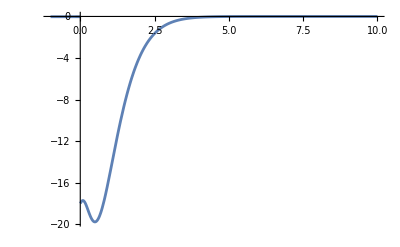

```mathematica
Plot[segnaleGraf[t], {t,-1,10}, PlotRange->All]
```